## Basic information;

```mathematica
alatts={4.575,4.600,4.625,4.6583,4.685,4.730,4.759,4.801,4.850};
tempps={0,10,300,500,760,1000,1500,1900,2500,3200,3800};
temppps=tempps[[2;;11]];
temps2={300,300,760,1900,2500,3200,3800};
temps3={300,760,1900,2500,3200,3800};
temps4={10,300,760,1900,2500,3200,3800};
THz2meV=1/4.135665538536;K2meV=0.086173324;kjmol2evatom=1/(96.487*64);
Nat=64;Natvac=63;mass={91.224,12.0107,1};
ang2bohr=1/0.529177208;ev2har=1/27.211396;kB=1000*8.617332478*10^−5;
eVperAng2harperbohr=ev2har/ang2bohr;eVperAng22harperbohr2=ev2har/ang2bohr/ang2bohr;
HarBohr=meVperAng22harperbohr2=0.001*ev2har/ang2bohr/ang2bohr;
(*Constant, Fermi-Dirac and Fermi-Dirac changing with energy*)
K2eV=8.617332478*10^−5;
fermiDirac[energy_,temp_]:=1/(Exp[energy/(K2eV*temp)]+1)
(*define sigma and8 kappa kernels*)
(*temp in energy units*)
sigmaK[energy_,temp_]:=-D[fermiDirac[energy,temp],energy]
kappaK[energy_,temp_]:=-(1/temp)*(energy^2)*D[fermiDirac[energy,temp],energy]
eV2ryd=1/13.605698066;ryd2eV=13.605698066;
(*At QHA level note -
Vol=> 4.6583 4.685 4.730 4.759 4.801 4.850 is
temps=> 0noZP 754K 1884 2479 3185 3.822
*)
```

```mathematica
qhaVlist={4.6583,4.685,4.730,4.759,4.801,4.850};
qhaTlist={0,754,1884,2479,3185,3822};
```

## Import electron conductivity

```mathematica
(*DEFECT CONDUCTIVITY.../Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_primitive_ZrC_sigma_el*)
Import DOS;
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_primitive_ZrC_sigma_el"];
filesPrimSigmaEl={"prim.kp39.465837.trace", "prim.kp39.4685.trace", "prim.kp39.4730.trace", "prim.kp39.4759.trace", "prim.kp39.4801.trace", "prim.kp39.4850.trace"};
(*Exclude the DOS with zero smearing*)
importedPrimTrace=Table[ReadList[filesPrimSigmaEl[[i]],{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}],{i,1,filesPrimSigmaEl//Length}];
(*-rwxrwxrwx 1 tom staff 1.3M 15 Mar 10:43 prim.kp39.4801.transdos
1 # Ef[Ry] T[K] N DOS(Ef) S s/t R_H kappa0 c chi*)
```

```mathematica
Import transdos;
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_primitive_ZrC_sigma_el"];
filesPrimSigmaEldos={"prim.kp39.465837.transdos", "prim.kp39.4685.transdos", "prim.kp39.4730.transdos", "prim.kp39.4759.transdos", "prim.kp39.4801.transdos", "prim.kp39.4850.transdos"};
(*Exclude the DOS with zero smearing*)
importedPrimDOS=Table[ReadList[filesPrimSigmaEldos[[i]],{Number,Number,Number}],{i,1,filesPrimSigmaEldos//Length}];
(*1 #DOS(states/Ry/spin)-0.98542411E+00 0.12363563E+01 0.10000000E-03 0.00000000E+00 22218*)
```

```mathematica
Import v2dos;
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_primitive_ZrC_sigma_el"];
filesPrimSigmaElv2dos={"prim.kp39.465837.v2dos", "prim.kp39.4685.v2dos", "prim.kp39.4730.v2dos", "prim.kp39.4759.v2dos", "prim.kp39.4801.v2dos", "prim.kp39.4850.v2dos"};
(*Exclude the DOS with zero smearing*)
importedPrimv2dos=Table[ReadList[filesPrimSigmaElv2dos[[i]],{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}],{i,1,filesPrimSigmaElv2dos//Length}];
(*# Fermi veloc^2/Dos(e)*)
```

```mathematica
Parse the sigma_el files;
primSIGMAMoTau=Table[Table[{importedPrimTrace[[k]][[i]][[2]],importedPrimTrace[[k]][[i]][[6]]},{i,1,importedPrimTrace[[k]]//Length}][[1;;100]],{k,1,6}];
primKAPPAMoTau=Table[Table[{importedPrimTrace[[k]][[i]][[2]],importedPrimTrace[[k]][[i]][[8]]},{i,1,importedPrimTrace[[k]]//Length}][[1;;100]],{k,1,6}];
primDOS=Table[Table[{importedPrimDOS[[k]][[i]][[1]]*ryd2eV,importedPrimDOS[[k]][[i]][[2]]/ryd2eV},{i,1,importedPrimDOS[[k]]//Length}],{k,1,6}];
primV2DOS=Table[Table[{importedPrimv2dos[[k]][[i]][[1]]*ryd2eV,importedPrimv2dos[[k]][[i]][[2]]/ryd2eV},{i,1,importedPrimv2dos[[k]]//Length}],{k,1,6}];
```

#### Plot DOS v2DOS and sigma/tau;

-Graphics-

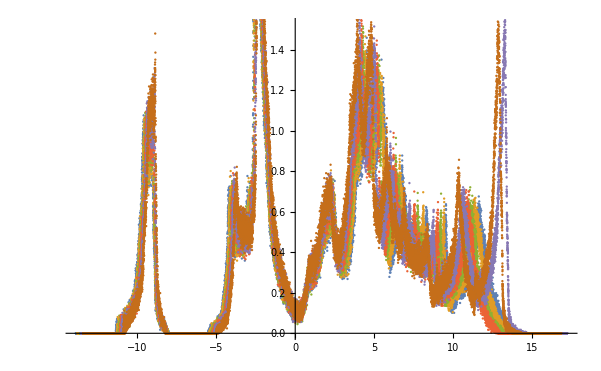

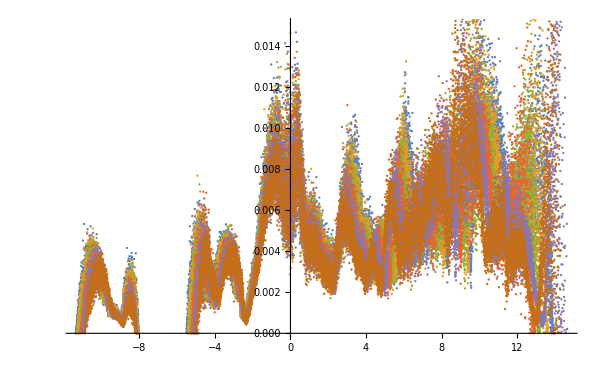

```mathematica
ListPlot[primSIGMAMoTau]
ListPlot@primDOS
ListPlot@primV2DOS
```

```mathematica
primSIGMAMoTauInter=Table[{40T,(1-((40*T-0)/(3810-0)))*Transpose[primSIGMAMoTau[[1]]][[2]][[T]]+(((40*T-0)/(3810-0)))*Transpose[primSIGMAMoTau[[6]]][[2]][[T]]},{T,1,4000/40}];
ListPlot[{primSIGMAMoTau[[1]],primSIGMAMoTau[[6]],primSIGMAMoTauInter}]
```

-Graphics-

```mathematica
primKAPPAMoTauInter=Table[{40T,(1-((40*T-0)/(3810-0)))*Transpose[primKAPPAMoTau[[1]]][[2]][[T]]+(((40*T-0)/(3810-0)))*Transpose[primKAPPAMoTau[[6]]][[2]][[T]]},{T,1,4000/40}];
ListPlot[{primKAPPAMoTau[[1]],primKAPPAMoTauInter,primKAPPAMoTau[[6]]}]
```

-Graphics-

#### Interpolate the DOS

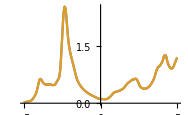

```mathematica
(*Doing a moving average, with window set to temperature*)
windowDOSfun[smearing_]:=(primDOS[[1]]//Length)*smearing/(Last[primDOS[[1]]][[1]]-First[primDOS[[1]]][[1]])*K2eV
DOSwindows=Table[Ceiling[windowDOSfun[qhaTlist[[i]]]+0.1],{i,1,qhaTlist//Length}];
dosWindowInter=Table[Interpolation[MovingAverage[primDOS[[i]],DOSwindows[[i]]]][x],{i,1,primDOS//Length}];
dosWindowInter2=Table[Interpolation[MovingMap[Mean,primDOS[[i]],{K2eV*(qhaTlist+1)[[i]],Center}]][x],{i,1,primDOS//Length}];
Plot[{dosWindowInter[[4]],dosWindowInter2[[4]]},{x,-5,5}]
```

```mathematica
plotOptsDOSinter={Frame->True,PlotRange->{{-5,5},All},AspectRatio->1, PlotTheme->"Scientific",FrameLabel->{Style["E (eV)",20],Style["g(E) (1/eV)",20]},FrameTicksStyle->20,ImageSize->400,PlotLegends->SwatchLegend[{Style["760 K",18],Style["1900 K",18],Style["2500 K",18],Style["3200 K",18],Style["3800 K",18]}]};

plotOptsV2DOS={ PlotTheme->"Scientific",PlotStyle->Directive[Orange,Opacity[0.25]],PlotStyle->PointSize[0.03],Frame->True,PlotRange->{{-5,5},All},AspectRatio->1,FrameLabel->{Style["E (eV)",20],Style["g(E) (1/eV)",20]},FrameTicksStyle->20,ImageSize->400};
```

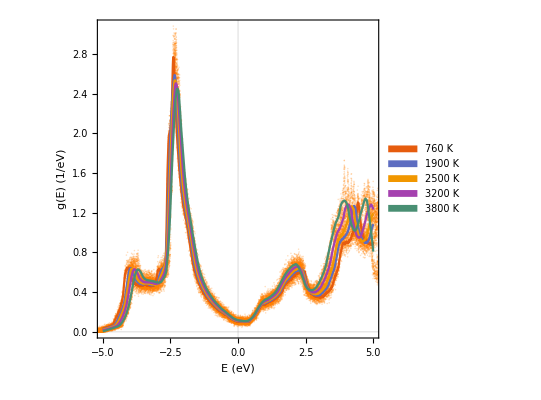

```mathematica
Show[{Table[ListPlot[primDOS[[i]],Evaluate@plotOptsV2DOS],{i,2,6}],Plot[Evaluate@dosWindowInter[[2;;6]],{x,-5,5},Evaluate@plotOptsDOSinter]}]
```

#### Interpolate the v2DOS;

```mathematica
(*Doing a moving average, with window set to temperature*)
windowDOSfun[smearing_]:=(primV2DOS[[1]]//Length)*smearing/(Last[primV2DOS[[1]]][[1]]-First[primV2DOS[[1]]][[1]])*K2eV
v2DOSwindows=Table[Ceiling[windowDOSfun[qhaTlist[[i]]]+0.1],{i,1,qhaTlist//Length}];
v2dosWindowInter=Table[Interpolation[MovingAverage[primV2DOS[[i]],v2DOSwindows[[i]]]][x],{i,1,primV2DOS//Length}];
v2dosWindowInter2=Table[Interpolation[MovingMap[Mean,primV2DOS[[i]],{K2eV*(qhaTlist+1)[[i]],Center}]][x],{i,1,primV2DOS//Length}];
```

```mathematica
v2dosWindowInter//Length
```

6

```mathematica
plotOptsV2DOSinter={Frame->True,PlotRange->{{-5,5},{0,0.012}},AspectRatio->1, PlotTheme->"Scientific",FrameLabel->{Style["E (eV)",20],Style["v^2/g(E)",20]},FrameTicksStyle->20,ImageSize->400,PlotLegends->SwatchLegend[{Style["760 K",18],Style["1900 K",18],Style["2500 K",18],Style["3200 K",18],Style["3800 K",18]}]};
plotOptsV2DOS={ PlotTheme->"Scientific",PlotStyle->Directive[Orange,Opacity[0.25]],PlotStyle->PointSize[0.03],Frame->True,PlotRange->{{-5,5},{0,0.012}},AspectRatio->1,FrameLabel->{Style["E (eV)",20],Style["v^2/g(E)",20]},FrameTicksStyle->20,ImageSize->400};
```

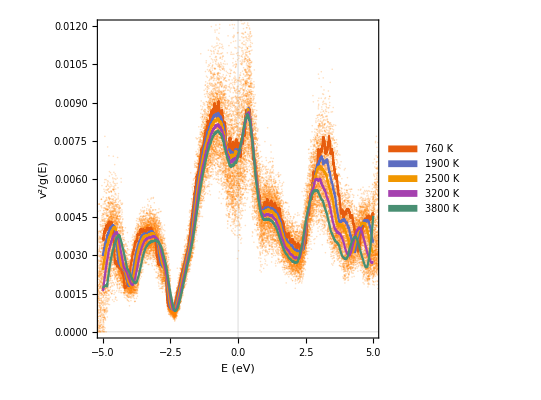

```mathematica
Show[{Table[ListPlot[primV2DOS[[i]],Evaluate@plotOptsV2DOS],{i,2,6}],Plot[Evaluate@v2dosWindowInter[[2;;6]],{x,-5,5},Evaluate@plotOptsV2DOSinter]}]
```

```mathematica
5
```

5

#### Plot DOS times v2DOS

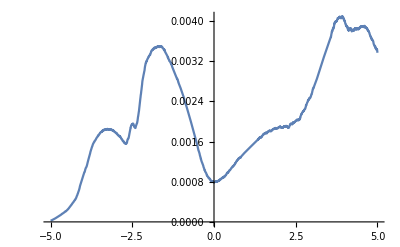

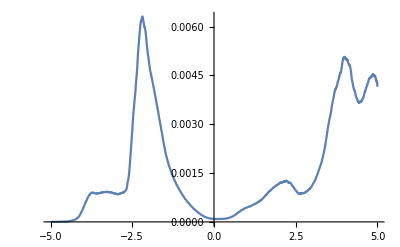

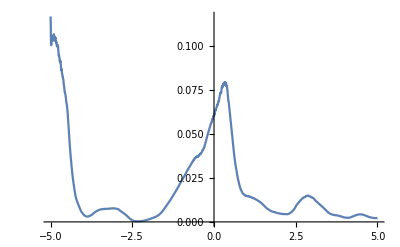

```mathematica
Plot[v2dosWindowInter[[5;;5]]*dosWindowInter[[5;;5]],{x,-5,5}]
Plot[v2dosWindowInter[[5;;5]]*dosWindowInter[[5;;5]]*dosWindowInter[[5;;5]],{x,-5,5}]
Plot[v2dosWindowInter[[5;;5]]/dosWindowInter[[5;;5]],{x,-5,5}]
```

```mathematica
dosWindowInter//Length
```

6

## Scattering Rates;

#### Get scattering Rates;

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/EPW/ZrC/LDA/"];
temps={"0K","10K","300K","500K","760K","1000K","1500K","1900K","2500K","3200K","3800K"};
scatteringRates=Table[ReadList[StringJoin["Variable_Volume/ScatteringRates/constant_smearing/kRandom/",ToString@temps[[i]],"/scattering_rate",ToString@temps[[i]]],{Number, Number,Number, Number,Number}],{i,1,11}];
```

#### Parse rates and lives;

```mathematica
rateData=Table[Transpose[{Transpose[scatteringRates[[i]]][[3]],Transpose[scatteringRates[[i]]][[4]]}],{i,1,11}];
lifeData=Table[Transpose[{Transpose[scatteringRates[[i]]][[3]],Transpose[1/scatteringRates[[i]]][[4]]}],{i,1,11}];
```

#### Downsample and plot lifetime and scattering rate;

```mathematica
rateDataR6=Table[RandomSample[rateData[[i]],0.15*10^6],{i,1,11}];
rateDataR5=Table[RandomSample[rateData[[i]],10^5],{i,1,11}];
rateDataR4=Table[RandomSample[rateData[[i]],10^4],{i,1,11}];
rateDataR3=Table[RandomSample[rateData[[i]],10^3],{i,1,11}];
rateDataR2=Table[RandomSample[rateData[[i]],10^2],{i,1,11}];
lifeDataR6=Table[RandomSample[lifeData[[i]],0.15*10^6],{i,1,11}];
lifeDataR5=Table[RandomSample[lifeData[[i]],10^5],{i,1,11}];
lifeDataR4=Table[RandomSample[lifeData[[i]],10^4],{i,1,11}];
lifeDataR3=Table[RandomSample[lifeData[[i]],10^3],{i,1,11}];
lifeDataR2=Table[RandomSample[lifeData[[i]],10^2],{i,1,11}];
```

```mathematica
plotOptsRates={FrameTicksStyle->20,Frame->True,ImageSize->400,FrameLabel->{Style["E-E_F(eV)",20],Style["Scattering rate (1/s)",20]},PlotRange->{All,{0,6*10^15}},AspectRatio->1,PlotTheme->"Scientific",PlotStyle->Directive[PointSize[0.000007]],PlotLegends->SwatchLegend[Table[Style[temps[[i]],20],{i,2,11,2}]]};
plotOptsLives={FrameTicksStyle->20,Frame->True,ImageSize->400,FrameLabel->{Style["E-E_F(eV)",20],Style["Lifetime tau (s)",20]},PlotRange->{{-5,5},{0,5*10^-14}},AspectRatio->1,PlotTheme->"Scientific",PlotStyle->Directive[PointSize[0.000007]],PlotLegends->SwatchLegend[Table[Style[temps[[i]],20],{i,2,11,2}]]};
```

```mathematica
ListPlot[Table[rateDataR5[[i]],{i,2,11,2}],Evaluate@plotOptsRates]
```

-Graphics-

```mathematica
ListPlot[Table[lifeDataR5[[i]],{i,2,11,2}],Evaluate@plotOptsLives]
```

-Graphics-

```mathematica
tempsScatter={1,10,300,500,760,1000,1500,1900,2500,3200,3800};
tempsScatterMixed300={300,300,300,500,760,1000,1500,1900,2500,3200,3800};
tempsScatterMixed100={100,100,300,500,760,1000,1500,1900,2500,3200,3800};
```

```mathematica
interRate=Table[Interpolation[MovingMap[Mean,{rateDataR4[[i]]},{K2eV*(tempsScatter[[i]]+1),Center}],InterpolationOrder->1,Method->"Hermite"],{i,1,11}];
```

```mathematica
interTau=Table[Interpolation[MovingMap[Mean,{lifeDataR4[[i]]},{K2eV*(tempsScatter[[i]]+1),Center}],InterpolationOrder->1,Method->"Hermite"],{i,1,11}];
```

```mathematica
interTau0010=Table[Interpolation[MovingMap[Mean,{lifeDataR4[[i]]},{K2eV*(0.01),Center}],InterpolationOrder->1,Method->"Hermite"],{i,1,11}];
```

```mathematica
interTauMixed300=Table[Interpolation[MovingMap[Mean,{lifeDataR4[[i]]},{K2eV*tempsScatterMixed300[[i]]+1,Center}],InterpolationOrder->1,Method->"Hermite"],{i,1,11}];
```

```mathematica
interTauMixed100=Table[Interpolation[MovingMap[Mean,{lifeDataR4[[i]]},{K2eV*tempsScatterMixed100[[i]]+1,Center}],InterpolationOrder->1,Method->"Hermite"],{i,1,11}];
```

```mathematica
K2eV*(tempsScatter)
```

{0.0000861733,0.000861733,0.025852,0.0430867,0.0654917,0.0861733,0.12926,0.163729,0.215433,0.275755,0.327459}

#### Plot lifetime tau;

```mathematica
plotOptsTauRates={FrameTicksStyle->20,Frame->True,ImageSize->400,FrameLabel->{Style["E-E_F(eV)",20],Style["Scattering rate (1/s)",20]},PlotRange->{All,{0,6*10^15}},AspectRatio->1,PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.007]],PlotLegends->SwatchLegend[Table[Style[temps[[i]],20],{i,1,11}]]};
plotOptsTauLives={FrameTicksStyle->20,Frame->True,ImageSize->400,FrameLabel->{Style["E-E_F(eV)",20],Style["Lifetime tau (s)",20]},PlotRange->{{-5,5},{0,2.5*10^-14}},AspectRatio->1,PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.007]],PlotLegends->SwatchLegend[Table[Style[temps[[i+1]],20],{i,1,10}]]};
```

#### Scattering rate with smearing = temperature

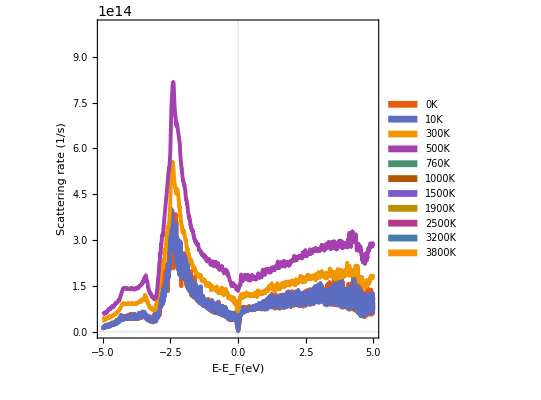

```mathematica
Plot[Evaluate@Table[interRate[[i]][x],{i,1,11}],{x,-5,5},Evaluate@plotOptsTauRates]
```

```mathematica
interTau//Length
```

11

#### lifetime with Smearing = temperature

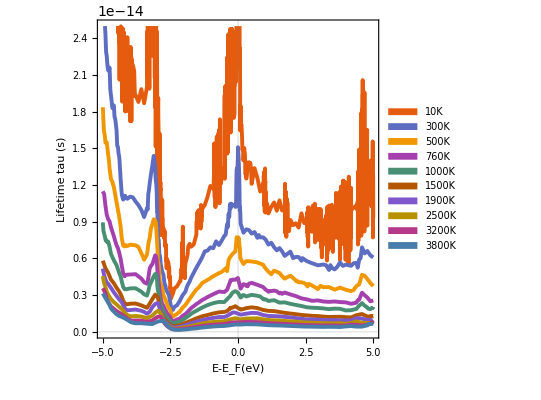

```mathematica
Plot[Evaluate@Table[interTau[[i]][x],{i,2,11}],{x,-5,5},Evaluate@plotOptsTauLives]
```

#### 0.01eV smearing

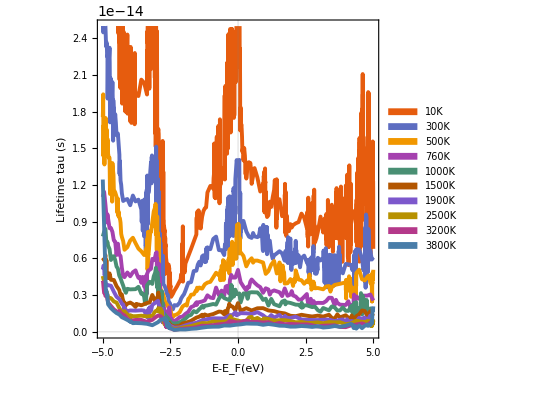

```mathematica
Plot[Evaluate@Table[interTau0010[[i]][x],{i,2,11}],{x,-5,5},Evaluate@plotOptsTauLives]
```

#### Mixed smearing

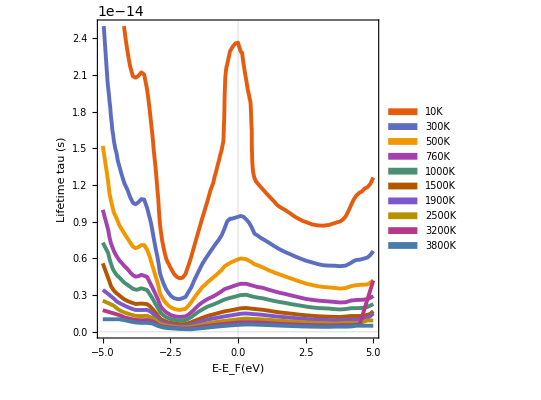

```mathematica
Plot[Evaluate@Table[interTauMixed100[[i]][x],{i,2,11}],{x,-5,5},Evaluate@plotOptsTauLives]
```

```mathematica
Plot[Evaluate@Table[interTauMixed100[[i]][x],{i,2,11}],{x,-5,5},Evaluate@plotOptsTauLives]
```

#### Plot kernel of convolution of lifetime and transport distribution function

Part::pkspec1: The expression i cannot be used as a part specification.

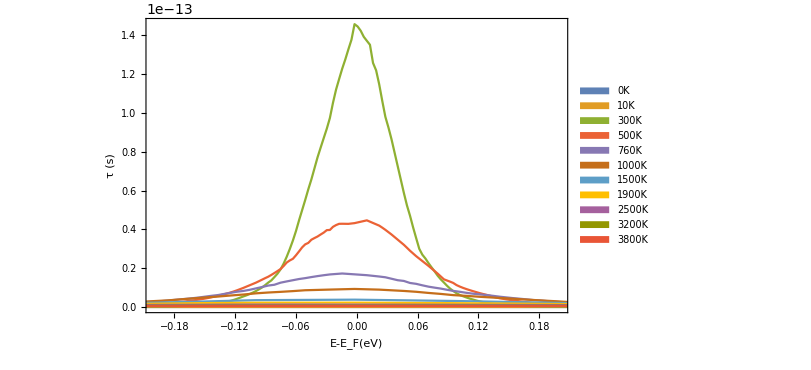

```mathematica
Plot[Evaluate@Table[Evaluate[sigmaK[x,tempsScatter[[i]]]*interTau[[i]][x]],{i,1,11}],{x,-5,5},PlotLegends->SwatchLegend[temps],Frame->True,FrameLabel->{"E-E_F(eV)","τ (s)"},ImageSize->600,PlotRange->{{-0.2,0.2},All}]
Off[s::Infinity::indet]
```

Part::pkspec1: The expression i cannot be used as a part specification.

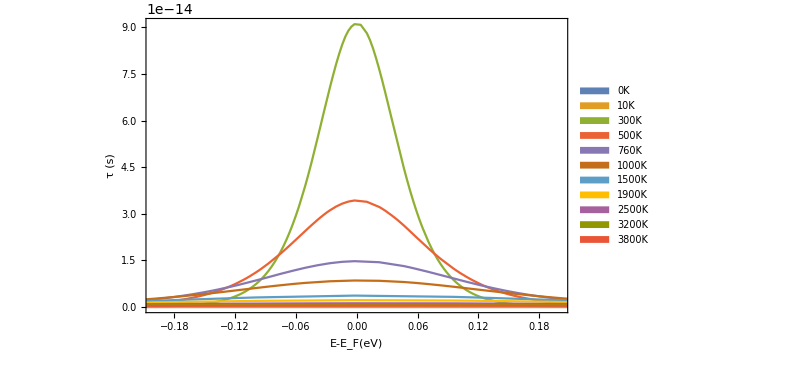

```mathematica
Plot[Evaluate@Table[Evaluate[sigmaK[x,tempsScatter[[i]]]*interTauMixed100[[i]][x]],{i,1,11}],{x,-5,5},PlotLegends->SwatchLegend[temps],Frame->True,FrameLabel->{"E-E_F(eV)","τ (s)"},ImageSize->600,PlotRange->{{-0.2,0.2},All}]
Off[s::Infinity::indet]
```

```mathematica
upper=5;lower=-5;
Off[s::NIntegrate::slwcon]
Off[s::General::stop]
Off[s::NIntegrate::eincr]
Off[s::General::stop]
meanTau=Table[(1/NIntegrate[1,{energy,-5,5}])*NIntegrate[interTau[[i]][energy],{energy,lower,upper},MaxRecursion->50,PrecisionGoal->20],{i,2,11}]
(*Note delta_T=1 added to the integral over f' to make it stable*)
Off[s::NIntegrate::slwcon]
Off[s::NIntegrate::eincr]
Off[s::NIntegrate::slwcon]
meanTauFD=Table[(1/NIntegrate[sigmaK[energy,tempsScatter[[i]]],{energy,-5,5}])*NIntegrate[interTau[[i]][energy]*sigmaK[energy,tempps[[i]]],{energy,lower,upper},MaxRecursion->50,PrecisionGoal->20],{i,2,11}]
Off[s::NIntegrate::slwcon]
Off[s::NIntegrate::eincr]
Off[s::NIntegrate::slwcon]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.54643×10^-13 and 1.65516×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.78115×10^-14 and 2.97215×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.14925×10^-14 and 1.18601×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.4461×10^-14 and 5.86768×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.62429×10^-14 and 3.52134×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.72619×10^-14 and 1.59302×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.35895×10^-14 and 1.08137×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.00896×10^-14 and 6.29828×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.5945×10^-15 and 4.40688×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.13823×10^-15 and 3.03057×10^-20 for the integral and error estimates.

{1.54643×10^-14,7.78115×10^-15,5.14925×10^-15,3.4461×10^-15,2.62429×10^-15,1.72619×10^-15,1.35895×10^-15,1.00896×10^-15,7.5945×10^-16,6.13823×10^-16}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0193758}. NIntegrate obtained 0.500044 and 0.041055 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.4857×10^-13 and 4.5287×10^-29 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.30519×10^-14 and 6.94835×10^-29 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.07872×10^-15 and 7.74773×10^-27 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.12677×10^-15 and 5.704×10^-26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.09762×10^-15 and 8.77464×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.93078×10^-15 and 4.11605×10^-24 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.47092×10^-15 and 9.02142×10^-24 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.04354×10^-15 and 2.41786×10^-23 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.53767×10^-16 and 6.10138×10^-23 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.62902×10^-16 and 8.88215×10^-23 for the integral and error estimates.

{6.97079×10^-13,1.30519×10^-14,7.07872×10^-15,4.12677×10^-15,3.09762×10^-15,1.93078×10^-15,1.47092×10^-15,1.04354×10^-15,7.53767×10^-16,5.62902×10^-16}

```mathematica
meanTauFD0010=Table[(1/NIntegrate[sigmaK[energy,tempsScatter[[i]]],{energy,-5,5}])*NIntegrate[interTau0010[[i]][energy]*sigmaK[energy,tempps[[i]]],{energy,lower,upper},MaxRecursion->50,PrecisionGoal->20],{i,2,11}]
Off[s::NIntegrate::slwcon]
Off[s::NIntegrate::eincr]
Off[s::NIntegrate::slwcon]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0193758}. NIntegrate obtained 0.500044 and 0.041055 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.4857×10^-13 and 4.5287×10^-29 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.31962×10^-14 and 5.27694×10^-27 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.14608×10^-15 and 5.63501×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.1303×10^-15 and 1.22724×10^-23 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.11935×10^-15 and 1.48876×10^-22 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.9301×10^-15 and 1.23288×10^-21 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.47611×10^-15 and 3.33586×10^-21 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.04764×10^-15 and 1.18322×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.53439×10^-16 and 3.8245×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.62227×10^-16 and 4.34287×10^-20 for the integral and error estimates.

{6.97079×10^-13,1.31962×10^-14,7.14608×10^-15,4.1303×10^-15,3.11935×10^-15,1.9301×10^-15,1.47611×10^-15,1.04764×10^-15,7.53439×10^-16,5.62227×10^-16}

```mathematica
tempps
```

{0,10,300,500,760,1000,1500,1900,2500,3200,3800}

```mathematica
fv2dos0=(v2dosWindowInter[[5;;5]])/.x->energy;
fv2dos1=(v2dosWindowInter[[5;;5]]/dosWindowInter[[5;;5]])/.x->energy;
fv2dos2=(v2dosWindowInter[[5;;5]]*dosWindowInter[[5;;5]])/.x->energy;
fv2dos3=(v2dosWindowInter[[5;;5]]*dosWindowInter[[5;;5]]*dosWindowInter[[5;;5]])/.x->energy;
```

```mathematica
meanTauFDv2f1=Table[(1/NIntegrate[fv2dos1*sigmaK[energy,tempsScatter[[i]]],{energy,-5,5}])*NIntegrate[interTau[[i]][energy]*fv2dos1*sigmaK[energy,tempsScatter[[i]]],{energy,lower,upper},MaxRecursion->50,PrecisionGoal->20],{i,2,11}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0193758}. NIntegrate obtained 0.0300297 and 0.00243266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.09442×10^-14 and 2.74922×10^-30 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0389071}. NIntegrate obtained 0.0607001 and 0.0000330577 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.91307×10^-16 and 3.0884×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0389071}. NIntegrate obtained 0.0607487 and 0.0000376069 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.29048×10^-16 and 1.57657×10^-24 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {-0.0196867}. NIntegrate obtained 0.0607115 and 0.0000174993 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.49458×10^-16 and 6.37545×10^-24 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0389071}. NIntegrate obtained 0.0605574 and 0.000029929 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.86946×10^-16 and 8.69685×10^-24 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {-0.0196867}. NIntegrate obtained 0.0594124 and 0.0000132051 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.14813×10^-16 and 1.65127×10^-23 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0389071}. NIntegrate obtained 0.0578495 and 0.0000223903 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.54791×10^-17 and 1.78762×10^-23 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0389071}. NIntegrate obtained 0.054883 and 0.0000192661 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.80137×10^-17 and 2.01242×10^-23 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0389071}. NIntegrate obtained 0.0511304 and 0.0000174537 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.95521×10^-17 and 1.83316×10^-23 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0389071}. NIntegrate obtained 0.0480006 and 0.0000156962 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.80596×10^-17 and 1.6458×10^-23 for the integral and error estimates.

{{6.97451×10^-13},{1.30363×10^-14},{7.06266×10^-15},{4.10891×10^-15},{3.08709×10^-15},{1.93248×10^-15},{1.47761×10^-15},{1.05704×10^-15},{7.73552×10^-16},{5.84568×10^-16}}

```mathematica
meanTauFDv2f2=Table[(1/NIntegrate[fv2dos2*sigmaK[energy,tempsScatter[[i]]],{energy,-5,5}])*NIntegrate[interTau[[i]][energy]*fv2dos2*sigmaK[energy,tempsScatter[[i]]],{energy,lower,upper},MaxRecursion->50,PrecisionGoal->20],{i,2,11}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {-0.000155416}. NIntegrate obtained 0.000395568 and 0.0000322716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.75172×10^-16 and 4.09273×10^-32 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0193758}. NIntegrate obtained 0.000800607 and 2.4299×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.04378×10^-17 and 4.47998×10^-27 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0193758}. NIntegrate obtained 0.000809541 and 2.44608×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.72182×10^-18 and 2.51205×10^-26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {-0.0978117}. NIntegrate obtained 0.000826278 and 2.30194×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.4063×10^-18 and 1.03126×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {-0.0978117}. NIntegrate obtained 0.000846656 and 2.34886×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.61708×10^-18 and 1.87984×10^-25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {-0.0978117}. NIntegrate obtained 0.000901776 and 2.67951×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.72991×10^-18 and 4.01315×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {-0.0978117}. NIntegrate obtained 0.000954777 and 2.3608×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.38778×10^-18 and 5.69644×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {-0.0978117}. NIntegrate obtained 0.00104232 and 2.2473×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.06129×10^-18 and 7.56085×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.117032}. NIntegrate obtained 0.0011484 and 1.95553×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.31012×10^-19 and 8.75519×10^-25 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {-0.0978117}. NIntegrate obtained 0.00123625 and 2.49827×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.58513×10^-19 and 9.84092×10^-25 for the integral and error estimates.

{{6.95637×10^-13},{1.30374×10^-14},{7.06798×10^-15},{4.12246×10^-15},{3.09108×10^-15},{1.91833×10^-15},{1.45351×10^-15},{1.0182×10^-15},{7.23628×10^-16},{5.32668×10^-16}}

```mathematica
meanTauFDv2f3=Table[(1/NIntegrate[fv2dos3*sigmaK[energy,tempsScatter[[i]]],{energy,-5,5}])*NIntegrate[interTau[[i]][energy]*fv2dos3*sigmaK[energy,tempsScatter[[i]]],{energy,lower,upper},MaxRecursion->50,PrecisionGoal->20],{i,2,11}]
```

{{6.95191×10^-13},{1.30348×10^-14},{7.06825×10^-15},{4.12723×10^-15},{3.08754×10^-15},{1.89974×10^-15},{1.42461×10^-15},{9.75545×10^-16},{6.68369×10^-16},{4.74737×10^-16}}

```mathematica
meanTauFDv2f0Mixed100=Table[(1/NIntegrate[fv2dos0*sigmaK[energy,tempsScatter[[i]]],{energy,-5,5}])*NIntegrate[interTauMixed100[[i]][energy]*fv2dos0*sigmaK[energy,tempsScatter[[i]]],{energy,lower,upper},MaxRecursion->50,PrecisionGoal->20],{i,2,11}]
```

{{4.73336×10^-14},{9.43193×10^-15},{5.91424×10^-15},{3.86148×10^-15},{2.93922×10^-15},{1.87132×10^-15},{1.42515×10^-15},{1.00732×10^-15},{7.29561×10^-16},{5.42336×10^-16}}

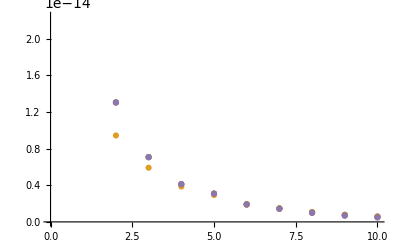

```mathematica
Show[{ListPlot@{Flatten@meanTauFDv2f1,Flatten@meanTauFDv2f0Mixed100,Flatten@meanTauFDv2f1,Flatten@meanTauFDv2f2,Flatten@meanTauFDv2f3}}]
```

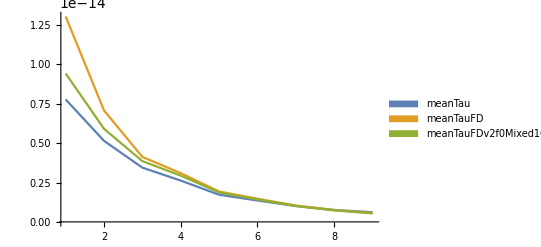

```mathematica
ListLinePlot[{meanTau[[2;;10]],meanTauFD[[2;;10]],Flatten@meanTauFDv2f0Mixed100[[2;;10]]},PlotRange->All,PlotLegends->SwatchLegend[{"meanTau","meanTauFD","meanTauFDv2f0Mixed100"}]]
```

```mathematica
tmeanTau=Transpose[{tempsScatter[[2;;11]],meanTau[[1;;10]]}];
tmeanTauFD=Transpose[{tempsScatter[[2;;11]],meanTauFD[[1;;10]]}];
tmeanTauFDmix100=Transpose[{tempsScatter[[2;;11]],Flatten@meanTauFDv2f0Mixed100[[1;;10]]}];


(*Interpolation*)
tmeanTauInter=Interpolation[tmeanTau,InterpolationOrder->3];
tmeanTauInterFD=Interpolation[tmeanTauFD,InterpolationOrder->1];
tmeanTauInterFDmix100=Interpolation[tmeanTauFDmix100,InterpolationOrder->1];
```

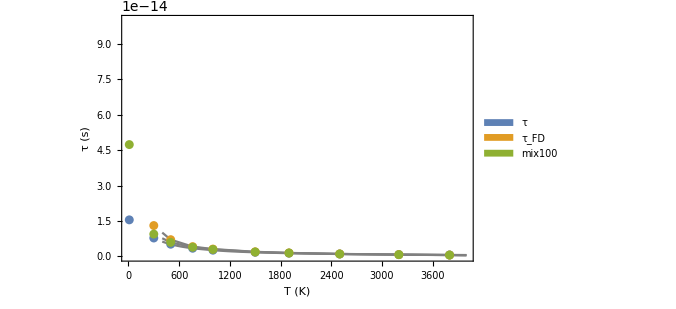

```mathematica
Show[Plot[Evaluate[{tmeanTauInter[x],tmeanTauInterFD[x],tmeanTauInterFDmix100[x]}],{x,400,4000},PlotRange->{{0,4000},{0,10^-13}},PlotStyle->Gray,Frame->True,FrameLabel->{"T (K)","τ (s)"},ImageSize->500],ListPlot[{tmeanTau,tmeanTauFD,tmeanTauFDmix100},PlotLegends->SwatchLegend[{"τ","τ_FD","mix100"}]]]
```

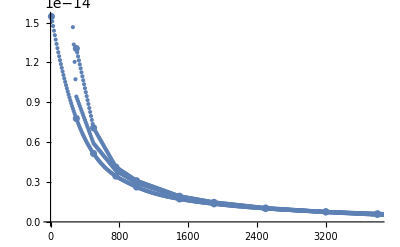

```mathematica
tmeanTauInter10=Table[{i,tmeanTauInter[i]},{i,10,4000,10}];
tmeanTauInterFD10=Table[{i,tmeanTauInterFD[i]},{i,10,4000,10}];
tmeanTauInterFD10mix100=Table[{i,tmeanTauInterFDmix100[i]},{i,10,4000,10}];
Show[{ListPlot@tmeanTauInter,ListPlot@tmeanTauInter10},{ListPlot@tmeanTauInterFD,ListPlot@tmeanTauInterFD10},{ListPlot@tmeanTauInterFD10mix100}]
```

```mathematica
primSIGMAMoTauInter10=Table[{i,Interpolation[primSIGMAMoTauInter][i]},{i,10,4000,10}];
primSIGMAMoTau300Inter10=Table[{i,Interpolation[primSIGMAMoTau[[2]]][i]},{i,10,4000,10}];
primSIGMAMoTau3800Inter10=Table[{i,Interpolation[primSIGMAMoTau[[-1]]][i]},{i,10,4000,10}];
Show[{ListPlot[{primSIGMAMoTauInter,primSIGMAMoTau300Inter10,primSIGMAMoTau3800Inter10}],Plot[Interpolation[primSIGMAMoTauInter][x],{x,1,4000}]}]
```

-Graphics-

```mathematica
primKAPPAMoTauInter10=Table[{i,Interpolation[primKAPPAMoTauInter][i]},{i,10,4000,10}];
primKAPPAMoTau300Inter10=Table[{i,Interpolation[primKAPPAMoTau[[2]]][i]},{i,10,4000,10}];
primKAPPAMoTau3800Inter10=Table[{i,Interpolation[primKAPPAMoTau[[-1]]][i]},{i,10,4000,10}];
Show[{ListPlot[{primKAPPAMoTauInter,primKAPPAMoTau300Inter10,primKAPPAMoTau3800Inter10}],Plot[Interpolation[primKAPPAMoTauInter][x],{x,1,4000}]}]
```

-Graphics-

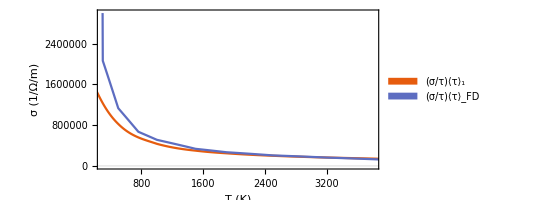

```mathematica
plotOptsSigma={PlotRange->{{300,3800},{0,3000000}},AspectRatio->0.5,
PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["T (K)",20],Style["σ (1/Ω/m)",20]},FrameTicksStyle->20,ImageSize->400,PlotLegends->SwatchLegend[{Style["(σ/τ)⟨τ⟩_1",18],Style["(σ/τ)⟨τ⟩_FD",18]}]};
plotSigma1=ListLinePlot[{Transpose[{Transpose[tmeanTauInter10][[1]],Transpose[primSIGMAMoTauInter10][[2]]*Transpose[tmeanTauInter10][[2]]}],Transpose[{Transpose[tmeanTauInterFD10][[1]],Transpose[primSIGMAMoTauInter10][[2]]*Transpose[tmeanTauInterFD10][[2]]}]},Evaluate@plotOptsSigma]
```

#### old data

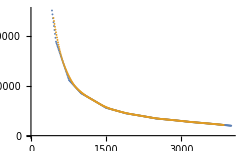

```mathematica
sigmaZrCdata=Transpose[{Transpose[tmeanTauInterFD10][[1]],Transpose[primSIGMAMoTauInter10][[2]]*Transpose[tmeanTauInterFD10][[2]]}];
sigmaZrCdataSmooth=MovingMap[Mean,sigmaZrCdata,{300,Center}];
ListPlot[{sigmaZrCdata,sigmaZrCdataSmooth}]
```

### new sigma el data

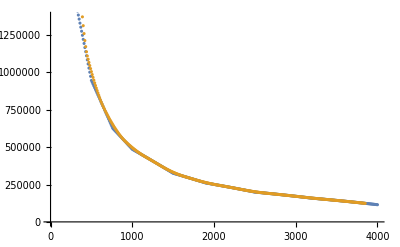

```mathematica
sigmaZrCdata2=Transpose[{Transpose[tmeanTauInterFD10mix100][[1]],Transpose[primSIGMAMoTauInter10][[2]]*Transpose[tmeanTauInterFD10mix100][[2]]}];
sigmaZrCdataSmooth2=MovingMap[Mean,sigmaZrCdata2,{300,Center}];
ListPlot[{sigmaZrCdata2,sigmaZrCdataSmooth2}]
```

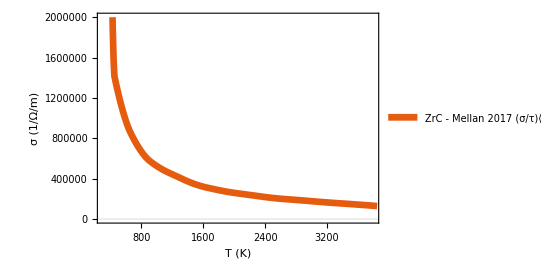

```mathematica
plotOptsSigma2={PlotRange->{{300,3800},{0,2000000}},AspectRatio->0.66,PlotStyle->Thickness[0.012],
PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["T (K)",20],Style["σ (1/Ω/m)",20]},FrameTicksStyle->20,ImageSize->400,PlotLegends->SwatchLegend[{Style["ZrC - Mellan 2017 \n (σ/τ)⟨τ⟩_FD",18]}]};
plotSigmaMe=ListLinePlot[sigmaZrCdataSmooth,Evaluate@plotOptsSigma2]
```

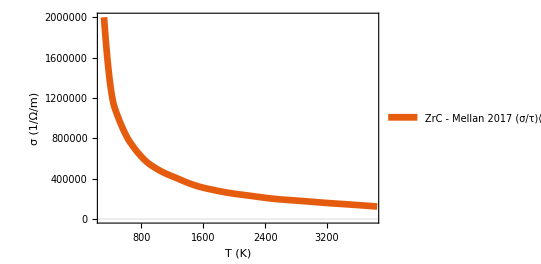

```mathematica
plotOptsSigma2={PlotRange->{{300,3800},{0,2000000}},AspectRatio->0.66,PlotStyle->Thickness[0.012],
PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["T (K)",20],Style["σ (1/Ω/m)",20]},FrameTicksStyle->20,ImageSize->400,PlotLegends->SwatchLegend[{Style["ZrC - Mellan 2017 \n (σ/τ)⟨τ⟩_FD",18]}]};
plotSigmaMe2=ListLinePlot[sigmaZrCdataSmooth2,Evaluate@plotOptsSigma2]
```

#### Plot kappa_el

```mathematica
Transpose[tmeanTauInter10][[2]]//Length
```

400

ListPlot::lpn: primKAPPAMoTauInter10 is not a list of numbers or pairs of numbers.

ListPlot[primKAPPAMoTauInter10]

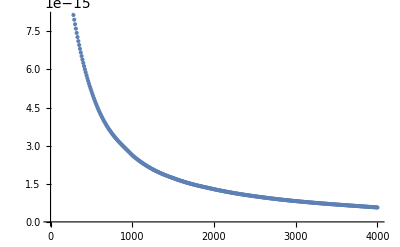

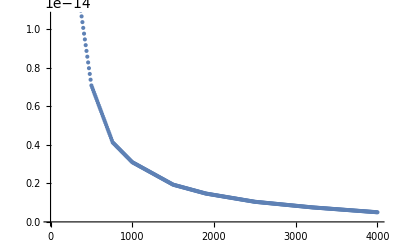

Part::partw: Part 2 of Transpose[primKAPPAMoTauInter10] does not exist.

-Graphics-

Part::partw: Part 2 of Transpose[primKAPPAMoTauInter10] does not exist.

-Graphics-

```mathematica
ListPlot@primKAPPAMoTauInter10
ListPlot@tmeanTauInter10
ListPlot@tmeanTauInterFD10
ListLinePlot@Transpose[{Transpose[tmeanTauInter10][[1]],Transpose[tmeanTauInter10][[2]]*Transpose[primKAPPAMoTauInter10][[2]]}]
ListLinePlot@Transpose[{Transpose[tmeanTauInterFD10][[1]],Transpose[tmeanTauInterFD10][[2]]*Transpose[primKAPPAMoTauInter10][[2]]}]
```

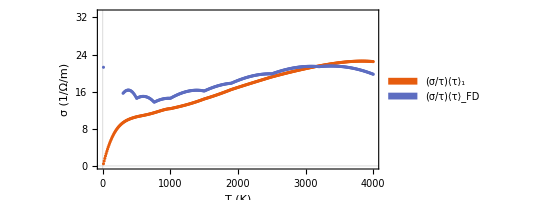

```mathematica
primKAPPAMoTauInter10=Table[{i,Interpolation[primKAPPAMoTauInter][i]},{i,10,4000,10}];
plotOptsKappa={AspectRatio->0.5,
PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["T (K)",20],Style["σ (1/Ω/m)",20]},FrameTicksStyle->20,ImageSize->400,PlotLegends->SwatchLegend[{Style["(σ/τ)⟨τ⟩_1",18],Style["(σ/τ)⟨τ⟩_FD",18]}]};
plotKappa1=ListPlot[{Transpose[{Transpose[tmeanTauInter10][[1]],Transpose[primKAPPAMoTauInter10][[2]]*Transpose[tmeanTauInter10][[2]]}],Transpose[{Transpose[tmeanTauInterFD10][[1]],Transpose[primKAPPAMoTauInter10][[2]]*Transpose[tmeanTauInterFD10][[2]]}]},Evaluate@plotOptsKappa]
```

#### Import experimental sigma_el

```mathematica
SetDirectory["/Users/tom/Documents/ZrC_experimental_sigma/"];
filesExpSigma={"Samsonov_ZrC.txt", "Grossman_ZrC.txt", "Neshpoor_ZrC.txt", "Taylor_ZrC0.94.txt"};
(*Exclude the DOS with zero smearing*)
ExpSigmaRaw=Table[ReadList[filesExpSigma[[i]],{Number,Number}],{i,1,filesExpSigma//Length}];
```

```mathematica
(*Experimental ZrC sigma_el data*)
```

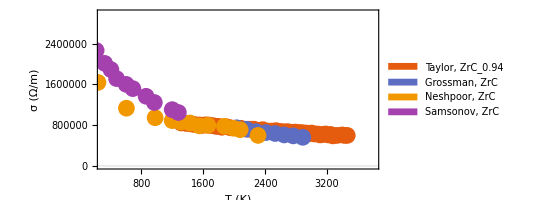

```mathematica
SigmaExp=Table[Transpose[{Transpose[ExpSigmaRaw[[i]]][[1]],
10000*Transpose[ExpSigmaRaw[[i]]][[2]]}],{i,1,4}];
plotOptsSigmaExp={PlotRange->{{300,3800},{0,3000000}},AspectRatio->0.5,
PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["T (K)",20],Style["σ (Ω/m)",20]},FrameTicksStyle->20,ImageSize->400,PlotStyle->PointSize[0.03],PlotLegends->SwatchLegend[{Style["Taylor, ZrC_0.94",18],Style["Grossman, ZrC",18],Style["Neshpoor, ZrC",18],Style["Samsonov, ZrC",18]}]};
plotSigmaExp=ListPlot[SigmaExp,Evaluate@plotOptsSigmaExp]
```

#### Crocombette theoretical data

{{1000,1.30646×10^6},{1500,947418.},{2000,820546.},{2500,672224.},{3000,578001.}}

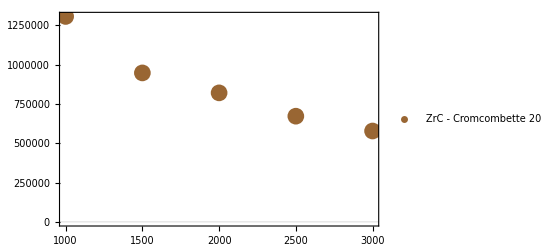

```mathematica
rhoCroc={7.6543*10^-7,1.0555*10^-6,1.2187*10^-6,1.4876*10^-6,1.7301*10^-6};
sigmElCroc=1/rhoCroc;
tempsCroc={1000,1500,2000,2500,3000};
sigmaCroc=Transpose[{tempsCroc,sigmElCroc}]
plotCrocSigma=ListPlot[sigmaCroc,PlotStyle->Directive[PointSize[0.03],Brown],PlotTheme->"Scientific",PlotLegends->{Style["ZrC - Cromcombette 2013",20]}]
```

#### Grossman data exp

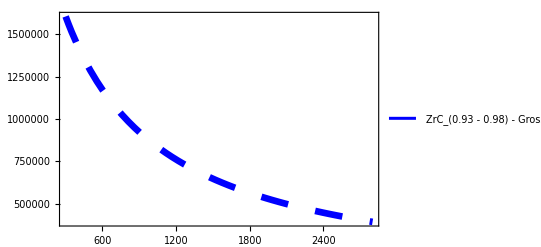

```mathematica
rhogGrossman[T_]:=1/(((0.393*10^-4)+(0.767*10^-7)*T)/100)
pGross=Plot[rhogGrossman[T],{T,300,2800},PlotStyle->Directive[Blue,Thickness[0.012],Dashing[0.05]],PlotTheme->"Scientific",PlotLegends->{Style["ZrC_(0.93 - 0.98) - Grossman 1965",20]}]
```

#### Import Savvatimsky

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/mathematica/Figures_papers/"];
filesSavvat={"savvatimskyDataSigmaEl.dat"};
(*Exclude the DOS with zero smearing*)
ExpSigmaSavvat=Table[ReadList[filesSavvat[[i]],{Number,Number}],{i,1,filesSavvat//Length}][[1]];
```

InterpolatingFunction[{{2093.07, 4897.22}}, <>]

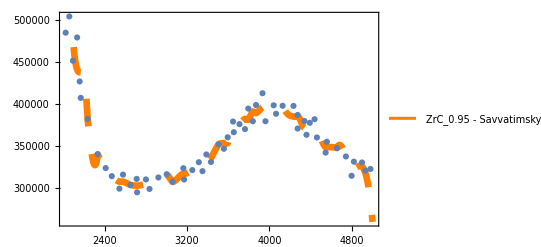

```mathematica
interSavvat=Interpolation[MovingMap[Mean,ExpSigmaSavvat,{100,Center}],InterpolationOrder->3]
pSavvat=Plot[interSavvat[x],{x,2100,5000},PlotRange->All,PlotTheme->"Scientific", PlotStyle->Directive[Dashing[0.05],Thickness[0.012],Orange],PlotLegends->{Style["ZrC_0.95 - Savvatimsky 2017",20]}];
p2Savvat=Show[{pSavvat,ListPlot[ExpSigmaSavvat]}]
```

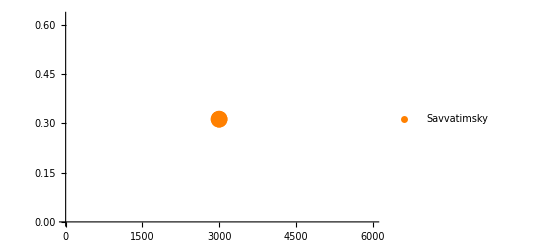

```mathematica
rhoSavvatimsky={{3000,0.3125}};
pSavvatold=ListPlot[rhoSavvatimsky,PlotStyle->Directive[Orange,PointSize[0.030],Dashing[Large]],PlotLegends->{"Savvatimsky"}]
```

## Final Plot of sigma el

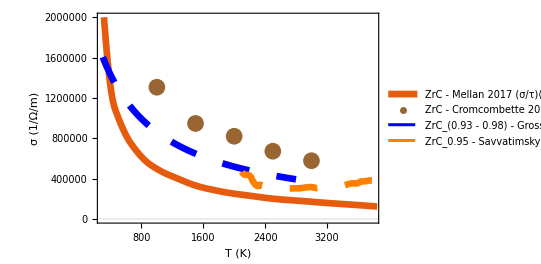

```mathematica
Show[{plotSigmaMe2,plotCrocSigma,pGross,pSavvat}]
```

```mathematica
(*Questions - Difference between Cromcombette and Us - 1) PBE, 2) Volume dependence, 3) Use Exp vol dependence or TU-TILD rather than QHA  *)
```

#### old plot

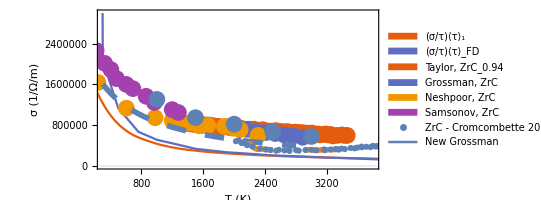

```mathematica
Show[{plotSigma1,plotSigmaExp,plotCrocSigma,pGross,p2Savvat}]
```